## Calculating the branching ratio for μ → e + γ,

```mathematica
s=11;BrDC=Table[0,{i,1,s},{j,1,s}];
```

```mathematica
l=1;
While[l<s+1,{f=2.5;W=3.5;K=5+l-1;v=0.17;
e1[t_,W_]:=RandomReal[{W,W},K]  (*No more a random list*);
g = e1[t,W];
Ox = Table[0,{x,2K},{y,2K}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = W,Ox[[i+K,i]] = W };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = W/f,Ox[[i+K,i+1]]=W/f};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = W*f ,Ox[[i+K+1,i]]=W*f};i++]
Ox;
ev1=Eigenvalues[Ox];
Eigenvectors[Ox][[-1]];
Ox1=Ox[[K+1;;2K,1;;K]];
{ou,ow,ov}=SingularValueDecomposition[SetPrecision[Ox1,35]];
A1 = v*Outer[Times,ou[[1]],ov[[1]]];
A2 = 3v*Outer[Times,ou[[1]],ov[[1]]];
A3 = 2v*Outer[Times,ou[[1]],ov[[1]]];
B1=A1+ow;
B2=A2+ow;
B3=A3+ow;
{bu1,bw1,bv1}=SingularValueDecomposition[SetPrecision[B1,50]];{bu2,bw2,bv2}=SingularValueDecomposition[SetPrecision[B2,50]];{bu3,bw3,bv3}=SingularValueDecomposition[SetPrecision[B3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K}];xe2 = Table[0,{i,1,K}];xe3 = Table[0,{i,1,K}];v=0.178;
i=1; While[i<K+1,{xe1[[i]] = Power[bw1[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+1,{xe2[[i]] = Power[bw2[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+1,{xe3[[i]] = Power[bw3[[i,i]]/Subscript[M, w],2]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K}];YM1 = Table[0,{i,1,K}];Fev2 = Table[0,{i,1,K}];YM2 = Table[0,{i,1,K}];Fev3 = Table[0,{i,1,K}];YM3 = Table[0,{i,1,K}];
i=1;While[i<K+1,{x=xe1[[i]],Fev1[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+1,{YM1[[i]] =bu1[[1,i]]*bu1[[1,i]]};i++];
i=1;While[i<K+1,{x=xe2[[i]],Fev2[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+1,{YM2[[i]] =bu2[[1,i]]*bu2[[1,i]]};i++];
i=1;While[i<K+1,{x=xe3[[i]],Fev3[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+1,{YM3[[i]] =bu3[[1,i]]*bu3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrDC[[1,l]]=BR = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
Ox1
```

(3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5 | 1.4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.75 | 3.5)

```mathematica
BrDC
```

(1.95078×10^-12 | 7.51272×10^-13 | 3.14544×10^-13 | 1.54909×10^-13 | 8.04841×10^-14 | 4.46581×10^-14 | 2.61213×10^-14 | 1.5968×10^-14 | 1.01341×10^-14 | 6.64171×10^-15 | 4.47596×10^-15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
BrE = Table[4.2*Power[10,-13],{i,1,s}]
```

{4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13,4.2×10^-13}

```mathematica
tcks = Table[i,{i,1,s}];
tc2=Table[{i,5+i-1},{i,1,s}];
```

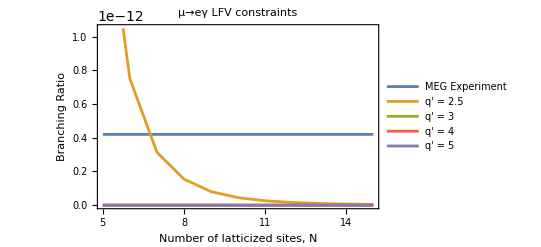

```mathematica
ListLinePlot[{BrE,BrDC[[1]],BrDC[[2]],BrDC[[3]],BrDC[[4]]},Ticks->{tcks, Automatic},PlotLegends->LineLegend[{"MEG Experiment","q' = 2.5","q' = 3","q' = 4","q' = 5"},LegendMarkerSize->10,LegendFunction->Frame],Frame->True,PlotLabel->Style["μ→eγ LFV constraints",Black],FrameLabel->{"Number of latticized sites, N","Branching Ratio"},LabelStyle->Directive[Black],FrameTicks->{{Automatic,None},{tc2,None}},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,s},Automatic}]
```

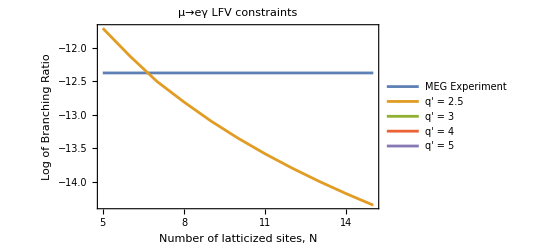

```mathematica
ListLinePlot[Log10[{BrE,BrDC[[1]],BrDC[[2]],BrDC[[3]],BrDC[[4]]}],Ticks->{tcks, Automatic},PlotLegends->LineLegend[{"MEG Experiment","q' = 2.5","q' = 3","q' = 4","q' = 5"},LegendMarkerSize->10,LegendFunction->Frame],Frame->True,PlotLabel->Style["μ→eγ LFV constraints",Black],FrameLabel->{"Number of latticized sites, N","Log of Branching Ratio"},LabelStyle->Directive[Black],FrameTicks->{{Automatic,None},{tc2,None}},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,s},Automatic}]
```